```mathematica
Practical - 1
```

```mathematica
IntegerQ[12]
True
ArrayQ[1]
False
pairQ[{ _,_}]:=True
pairQ[1]
pairQ[1]

pairQ[{1,2}]
True
pairQ[___]:= False
pairQ[2]
False
pairQ[ ]
False
relationQ[{___?pairQ}]:=True
relationQ[___]:=False
relationQ[{2,3,4}]
False
relationQ[{{2,3},{1,2}}]
True
Tuples[{1,2,6,5},2]
{{1,1},{1,2},{1,6},{1,5},{2,1},{2,2},{2,6},{2,5},{6,1},{6,2},{6,6},{6,5},{5,1},{5,2},{5,6},{5,5}}
Tuples[{1,2,6,5},3]
{{1,1,1},{1,1,2},{1,1,6},{1,1,5},{1,2,1},{1,2,2},{1,2,6},{1,2,5},{1,6,1},{1,6,2},{1,6,6},{1,6,5},{1,5,1},{1,5,2},{1,5,6},{1,5,5},{2,1,1},{2,1,2},{2,1,6},{2,1,5},{2,2,1},{2,2,2},{2,2,6},{2,2,5},{2,6,1},{2,6,2},{2,6,6},{2,6,5},{2,5,1},{2,5,2},{2,5,6},{2,5,5},{6,1,1},{6,1,2},{6,1,6},{6,1,5},{6,2,1},{6,2,2},{6,2,6},{6,2,5},{6,6,1},{6,6,2},{6,6,6},{6,6,5},{6,5,1},{6,5,2},{6,5,6},{6,5,5},{5,1,1},{5,1,2},{5,1,6},{5,1,5},{5,2,1},{5,2,2},{5,2,6},{5,2,5},{5,6,1},{5,6,2},{5,6,6},{5,6,5},{5,5,1},{5,5,2},{5,5,6},{5,5,5}}
dividesRelation[A:{___Integer}]:=Select[Tuples[A,2],Divisible[#[[2]],#[[1]]]&]

dividesRelation[{1,2,3}]
{{1,1},{1,2},{1,3},{2,2},{3,3}}
A={1,2,3,4,9,12}
dividesRelation[A]
{1,2,3,4,9,12}
{{1,1},{1,2},{1,3},{1,4},{1,9},{1,12},{2,2},{2,4},{2,12},{3,3},{3,9},{3,12},{4,4},{4,12},{9,9},{12,12}}
dividesRelation[Range[50]]
{{1,1},{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{1,10},{1,11},{1,12},{1,13},{1,14},{1,15},{1,16},{1,17},{1,18},{1,19},{1,20},{1,21},{1,22},{1,23},{1,24},{1,25},{1,26},{1,27},{1,28},{1,29},{1,30},{1,31},{1,32},{1,33},{1,34},{1,35},{1,36},{1,37},{1,38},{1,39},{1,40},{1,41},{1,42},{1,43},{1,44},{1,45},{1,46},{1,47},{1,48},{1,49},{1,50},{2,2},{2,4},{2,6},{2,8},{2,10},{2,12},{2,14},{2,16},{2,18},{2,20},{2,22},{2,24},{2,26},{2,28},{2,30},{2,32},{2,34},{2,36},{2,38},{2,40},{2,42},{2,44},{2,46},{2,48},{2,50},{3,3},{3,6},{3,9},{3,12},{3,15},{3,18},{3,21},{3,24},{3,27},{3,30},{3,33},{3,36},{3,39},{3,42},{3,45},{3,48},{4,4},{4,8},{4,12},{4,16},{4,20},{4,24},{4,28},{4,32},{4,36},{4,40},{4,44},{4,48},{5,5},{5,10},{5,15},{5,20},{5,25},{5,30},{5,35},{5,40},{5,45},{5,50},{6,6},{6,12},{6,18},{6,24},{6,30},{6,36},{6,42},{6,48},{7,7},{7,14},{7,21},{7,28},{7,35},{7,42},{7,49},{8,8},{8,16},{8,24},{8,32},{8,40},{8,48},{9,9},{9,18},{9,27},{9,36},{9,45},{10,10},{10,20},{10,30},{10,40},{10,50},{11,11},{11,22},{11,33},{11,44},{12,12},{12,24},{12,36},{12,48},{13,13},{13,26},{13,39},{14,14},{14,28},{14,42},{15,15},{15,30},{15,45},{16,16},{16,32},{16,48},{17,17},{17,34},{18,18},{18,36},{19,19},{19,38},{20,20},{20,40},{21,21},{21,42},{22,22},{22,44},{23,23},{23,46},{24,24},{24,48},{25,25},{25,50},{26,26},{27,27},{28,28},{29,29},{30,30},{31,31},{32,32},{33,33},{34,34},{35,35},{36,36},{37,37},{38,38},{39,39},{40,40},{41,41},{42,42},{43,43},{44,44},{45,45},{46,46},{47,47},{48,48},{49,49},{50,50}}
dividesRelation1[n_Integer]:=Select[Tuples[Range[n],2],Divisible[#[[2]],#[[1]]]&]
div10=dividesRelation1[10]
{{1,1},{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{1,10},{2,2},{2,4},{2,6},{2,8},{2,10},{3,3},{3,6},{3,9},{4,4},{4,8},{5,5},{5,10},{6,6},{7,7},{8,8},{9,9},{10,10}}
inverseRelation[R_?relationQ]:=Reverse[R,2]
inverseRelation[div10]
{{1,1},{2,1},{3,1},{4,1},{5,1},{6,1},{7,1},{8,1},{9,1},{10,1},{2,2},{4,2},{6,2},{8,2},{10,2},{3,3},{6,3},{9,3},{4,4},{8,4},{5,5},{10,5},{6,6},{7,7},{8,8},{9,9},{10,10}}
inverseRelation1[R_?relationQ]:=Reverse[R,1]
inverseRelation1[div10]
{{10,10},{9,9},{8,8},{7,7},{6,6},{5,10},{5,5},{4,8},{4,4},{3,9},{3,6},{3,3},{2,10},{2,8},{2,6},{2,4},{2,2},{1,10},{1,9},{1,8},{1,7},{1,6},{1,5},{1,4},{1,3},{1,2},{1,1}}
sumRelation[n_Integer]:=Select[Tuples[Range[n],2],#[[2]]+#[[1]]==10&]
sumRelation[20]
{{1,9},{2,8},{3,7},{4,6},{5,5},{6,4},{7,3},{8,2},{9,1}}
Subsets[{1,2,3}]
{{},{1},{2},{3},{1,2},{1,3},{2,3},{1,2,3}}
setincRelation[p_]:=Select[Tuples[Subsets[p],2],Intersection[#[[1]],#[[2]]]==#[[1]]&]
setincRelation[{1,2,3,4}]
{{{},{}},{{},{1}},{{},{2}},{{},{3}},{{},{4}},{{},{1,2}},{{},{1,3}},{{},{1,4}},{{},{2,3}},{{},{2,4}},{{},{3,4}},{{},{1,2,3}},{{},{1,2,4}},{{},{1,3,4}},{{},{2,3,4}},{{},{1,2,3,4}},{{1},{1}},{{1},{1,2}},{{1},{1,3}},{{1},{1,4}},{{1},{1,2,3}},{{1},{1,2,4}},{{1},{1,3,4}},{{1},{1,2,3,4}},{{2},{2}},{{2},{1,2}},{{2},{2,3}},{{2},{2,4}},{{2},{1,2,3}},{{2},{1,2,4}},{{2},{2,3,4}},{{2},{1,2,3,4}},{{3},{3}},{{3},{1,3}},{{3},{2,3}},{{3},{3,4}},{{3},{1,2,3}},{{3},{1,3,4}},{{3},{2,3,4}},{{3},{1,2,3,4}},{{4},{4}},{{4},{1,4}},{{4},{2,4}},{{4},{3,4}},{{4},{1,2,4}},{{4},{1,3,4}},{{4},{2,3,4}},{{4},{1,2,3,4}},{{1,2},{1,2}},{{1,2},{1,2,3}},{{1,2},{1,2,4}},{{1,2},{1,2,3,4}},{{1,3},{1,3}},{{1,3},{1,2,3}},{{1,3},{1,3,4}},{{1,3},{1,2,3,4}},{{1,4},{1,4}},{{1,4},{1,2,4}},{{1,4},{1,3,4}},{{1,4},{1,2,3,4}},{{2,3},{2,3}},{{2,3},{1,2,3}},{{2,3},{2,3,4}},{{2,3},{1,2,3,4}},{{2,4},{2,4}},{{2,4},{1,2,4}},{{2,4},{2,3,4}},{{2,4},{1,2,3,4}},{{3,4},{3,4}},{{3,4},{1,3,4}},{{3,4},{2,3,4}},{{3,4},{1,2,3,4}},{{1,2,3},{1,2,3}},{{1,2,3},{1,2,3,4}},{{1,2,4},{1,2,4}},{{1,2,4},{1,2,3,4}},{{1,3,4},{1,3,4}},{{1,3,4},{1,2,3,4}},{{2,3,4},{2,3,4}},{{2,3,4},{1,2,3,4}},{{1,2,3,4},{1,2,3,4}}}
setincRelation[Range[3]]
{{{},{}},{{},{1}},{{},{2}},{{},{3}},{{},{1,2}},{{},{1,3}},{{},{2,3}},{{},{1,2,3}},{{1},{1}},{{1},{1,2}},{{1},{1,3}},{{1},{1,2,3}},{{2},{2}},{{2},{1,2}},{{2},{2,3}},{{2},{1,2,3}},{{3},{3}},{{3},{1,3}},{{3},{2,3}},{{3},{1,2,3}},{{1,2},{1,2}},{{1,2},{1,2,3}},{{1,3},{1,3}},{{1,3},{1,2,3}},{{2,3},{2,3}},{{2,3},{1,2,3}},{{1,2,3},{1,2,3}}}
lessthanRelation[p_]:=Select[Tuples[Subsets[p],2],#[[1]]<#[[2]]&]
eqRelation[p_]:=Select[Tuples[Subsets[p],2],#[[1]]==#[[2]]&]
noteqRelation[p_]:=Select[Tuples[Subsets[p],2],#[[1]]!=#[[2]]&]
zRelation[p_]:=Select[Tuples[Subsets[p],2],#[[1]]==#[[2]]+1||#[[1]]==#[[2]]-1&]
a={1,2,3}
lessthanRelation[a]
eqRelation[a]
noteqRelation[a]
zRelation[a]
{1,2,3}
{}
{{{},{}},{{1},{1}},{{2},{2}},{{3},{3}},{{1,2},{1,2}},{{1,3},{1,3}},{{2,3},{2,3}},{{1,2,3},{1,2,3}}}
{{{},{1}},{{},{2}},{{},{3}},{{},{1,2}},{{},{1,3}},{{},{2,3}},{{},{1,2,3}},{{1},{}},{{1},{2}},{{1},{3}},{{1},{1,2}},{{1},{1,3}},{{1},{2,3}},{{1},{1,2,3}},{{2},{}},{{2},{1}},{{2},{3}},{{2},{1,2}},{{2},{1,3}},{{2},{2,3}},{{2},{1,2,3}},{{3},{}},{{3},{1}},{{3},{2}},{{3},{1,2}},{{3},{1,3}},{{3},{2,3}},{{3},{1,2,3}},{{1,2},{}},{{1,2},{1}},{{1,2},{2}},{{1,2},{3}},{{1,2},{1,3}},{{1,2},{2,3}},{{1,2},{1,2,3}},{{1,3},{}},{{1,3},{1}},{{1,3},{2}},{{1,3},{3}},{{1,3},{1,2}},{{1,3},{2,3}},{{1,3},{1,2,3}},{{2,3},{}},{{2,3},{1}},{{2,3},{2}},{{2,3},{3}},{{2,3},{1,2}},{{2,3},{1,3}},{{2,3},{1,2,3}},{{1,2,3},{}},{{1,2,3},{1}},{{1,2,3},{2}},{{1,2,3},{3}},{{1,2,3},{1,2}},{{1,2,3},{1,3}},{{1,2,3},{2,3}}}
{{{},{}},{{1},{2}},{{2},{1}},{{2},{3}},{{3},{2}},{{1,2},{2,3}},{{2,3},{1,2}}}
subset1={{1,2},{3,4},{1,4},{2,4}};
```

True

True

False

False

False

«1 more identical outputs»

True

True

False

False

False

«3 more identical outputs»

True

True

{{1,1},{1,2},{1,6},{1,5},{2,1},{2,2},{2,6},{2,5},{6,1},{6,2},{6,6},{6,5},{5,1},{5,2},{5,6},{5,5}}

{{1,1},{1,2},{1,6},{1,5},{2,1},{2,2},{2,6},{2,5},{6,1},{6,2},{6,6},{6,5},{5,1},{5,2},{5,6},{5,5}}

{{1,1,1},{1,1,2},{1,1,6},{1,1,5},{1,2,1},{1,2,2},{1,2,6},{1,2,5},{1,6,1},{1,6,2},{1,6,6},{1,6,5},{1,5,1},{1,5,2},{1,5,6},{1,5,5},{2,1,1},{2,1,2},{2,1,6},{2,1,5},{2,2,1},{2,2,2},{2,2,6},{2,2,5},{2,6,1},{2,6,2},{2,6,6},{2,6,5},{2,5,1},{2,5,2},{2,5,6},{2,5,5},{6,1,1},{6,1,2},{6,1,6},{6,1,5},{6,2,1},{6,2,2},{6,2,6},{6,2,5},{6,6,1},{6,6,2},{6,6,6},{6,6,5},{6,5,1},{6,5,2},{6,5,6},{6,5,5},{5,1,1},{5,1,2},{5,1,6},{5,1,5},{5,2,1},{5,2,2},{5,2,6},{5,2,5},{5,6,1},{5,6,2},{5,6,6},{5,6,5},{5,5,1},{5,5,2},{5,5,6},{5,5,5}}

{{1,1,1},{1,1,2},{1,1,6},{1,1,5},{1,2,1},{1,2,2},{1,2,6},{1,2,5},{1,6,1},{1,6,2},{1,6,6},{1,6,5},{1,5,1},{1,5,2},{1,5,6},{1,5,5},{2,1,1},{2,1,2},{2,1,6},{2,1,5},{2,2,1},{2,2,2},{2,2,6},{2,2,5},{2,6,1},{2,6,2},{2,6,6},{2,6,5},{2,5,1},{2,5,2},{2,5,6},{2,5,5},{6,1,1},{6,1,2},{6,1,6},{6,1,5},{6,2,1},{6,2,2},{6,2,6},{6,2,5},{6,6,1},{6,6,2},{6,6,6},{6,6,5},{6,5,1},{6,5,2},{6,5,6},{6,5,5},{5,1,1},{5,1,2},{5,1,6},{5,1,5},{5,2,1},{5,2,2},{5,2,6},{5,2,5},{5,6,1},{5,6,2},{5,6,6},{5,6,5},{5,5,1},{5,5,2},{5,5,6},{5,5,5}}

{{1,1},{1,2},{1,3},{2,2},{3,3}}

{{1,1},{1,2},{1,3},{2,2},{3,3}}

{1,2,3,4,9,12}

{{1,1},{1,2},{1,3},{1,4},{1,9},{1,12},{2,2},{2,4},{2,12},{3,3},{3,9},{3,12},{4,4},{4,12},{9,9},{12,12}}

{1,2,3,4,9,12}

{{1,1},{1,2},{1,3},{1,4},{1,9},{1,12},{2,2},{2,4},{2,12},{3,3},{3,9},{3,12},{4,4},{4,12},{9,9},{12,12}}

{{1,1},{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{1,10},{1,11},{1,12},{1,13},{1,14},{1,15},{1,16},{1,17},{1,18},{1,19},{1,20},{1,21},{1,22},{1,23},{1,24},{1,25},{1,26},{1,27},{1,28},{1,29},{1,30},{1,31},{1,32},{1,33},{1,34},{1,35},{1,36},{1,37},{1,38},{1,39},{1,40},{1,41},{1,42},{1,43},{1,44},{1,45},{1,46},{1,47},{1,48},{1,49},{1,50},{2,2},{2,4},{2,6},{2,8},{2,10},{2,12},{2,14},{2,16},{2,18},{2,20},{2,22},{2,24},{2,26},{2,28},{2,30},{2,32},{2,34},{2,36},{2,38},{2,40},{2,42},{2,44},{2,46},{2,48},{2,50},{3,3},{3,6},{3,9},{3,12},{3,15},{3,18},{3,21},{3,24},{3,27},{3,30},{3,33},{3,36},{3,39},{3,42},{3,45},{3,48},{4,4},{4,8},{4,12},{4,16},{4,20},{4,24},{4,28},{4,32},{4,36},{4,40},{4,44},{4,48},{5,5},{5,10},{5,15},{5,20},{5,25},{5,30},{5,35},{5,40},{5,45},{5,50},{6,6},{6,12},{6,18},{6,24},{6,30},{6,36},{6,42},{6,48},{7,7},{7,14},{7,21},{7,28},{7,35},{7,42},{7,49},{8,8},{8,16},{8,24},{8,32},{8,40},{8,48},{9,9},{9,18},{9,27},{9,36},{9,45},{10,10},{10,20},{10,30},{10,40},{10,50},{11,11},{11,22},{11,33},{11,44},{12,12},{12,24},{12,36},{12,48},{13,13},{13,26},{13,39},{14,14},{14,28},{14,42},{15,15},{15,30},{15,45},{16,16},{16,32},{16,48},{17,17},{17,34},{18,18},{18,36},{19,19},{19,38},{20,20},{20,40},{21,21},{21,42},{22,22},{22,44},{23,23},{23,46},{24,24},{24,48},{25,25},{25,50},{26,26},{27,27},{28,28},{29,29},{30,30},{31,31},{32,32},{33,33},{34,34},{35,35},{36,36},{37,37},{38,38},{39,39},{40,40},{41,41},{42,42},{43,43},{44,44},{45,45},{46,46},{47,47},{48,48},{49,49},{50,50}}

{{1,1},{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{1,10},{1,11},{1,12},{1,13},{1,14},{1,15},{1,16},{1,17},{1,18},{1,19},{1,20},{1,21},{1,22},{1,23},{1,24},{1,25},{1,26},{1,27},{1,28},{1,29},{1,30},{1,31},{1,32},{1,33},{1,34},{1,35},{1,36},{1,37},{1,38},{1,39},{1,40},{1,41},{1,42},{1,43},{1,44},{1,45},{1,46},{1,47},{1,48},{1,49},{1,50},{2,2},{2,4},{2,6},{2,8},{2,10},{2,12},{2,14},{2,16},{2,18},{2,20},{2,22},{2,24},{2,26},{2,28},{2,30},{2,32},{2,34},{2,36},{2,38},{2,40},{2,42},{2,44},{2,46},{2,48},{2,50},{3,3},{3,6},{3,9},{3,12},{3,15},{3,18},{3,21},{3,24},{3,27},{3,30},{3,33},{3,36},{3,39},{3,42},{3,45},{3,48},{4,4},{4,8},{4,12},{4,16},{4,20},{4,24},{4,28},{4,32},{4,36},{4,40},{4,44},{4,48},{5,5},{5,10},{5,15},{5,20},{5,25},{5,30},{5,35},{5,40},{5,45},{5,50},{6,6},{6,12},{6,18},{6,24},{6,30},{6,36},{6,42},{6,48},{7,7},{7,14},{7,21},{7,28},{7,35},{7,42},{7,49},{8,8},{8,16},{8,24},{8,32},{8,40},{8,48},{9,9},{9,18},{9,27},{9,36},{9,45},{10,10},{10,20},{10,30},{10,40},{10,50},{11,11},{11,22},{11,33},{11,44},{12,12},{12,24},{12,36},{12,48},{13,13},{13,26},{13,39},{14,14},{14,28},{14,42},{15,15},{15,30},{15,45},{16,16},{16,32},{16,48},{17,17},{17,34},{18,18},{18,36},{19,19},{19,38},{20,20},{20,40},{21,21},{21,42},{22,22},{22,44},{23,23},{23,46},{24,24},{24,48},{25,25},{25,50},{26,26},{27,27},{28,28},{29,29},{30,30},{31,31},{32,32},{33,33},{34,34},{35,35},{36,36},{37,37},{38,38},{39,39},{40,40},{41,41},{42,42},{43,43},{44,44},{45,45},{46,46},{47,47},{48,48},{49,49},{50,50}}

{{1,1},{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{1,10},{2,2},{2,4},{2,6},{2,8},{2,10},{3,3},{3,6},{3,9},{4,4},{4,8},{5,5},{5,10},{6,6},{7,7},{8,8},{9,9},{10,10}}

{{1,1},{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{1,10},{2,2},{2,4},{2,6},{2,8},{2,10},{3,3},{3,6},{3,9},{4,4},{4,8},{5,5},{5,10},{6,6},{7,7},{8,8},{9,9},{10,10}}

{{1,1},{2,1},{3,1},{4,1},{5,1},{6,1},{7,1},{8,1},{9,1},{10,1},{2,2},{4,2},{6,2},{8,2},{10,2},{3,3},{6,3},{9,3},{4,4},{8,4},{5,5},{10,5},{6,6},{7,7},{8,8},{9,9},{10,10}}

{{1,1},{2,1},{3,1},{4,1},{5,1},{6,1},{7,1},{8,1},{9,1},{10,1},{2,2},{4,2},{6,2},{8,2},{10,2},{3,3},{6,3},{9,3},{4,4},{8,4},{5,5},{10,5},{6,6},{7,7},{8,8},{9,9},{10,10}}

{{10,10},{9,9},{8,8},{7,7},{6,6},{5,10},{5,5},{4,8},{4,4},{3,9},{3,6},{3,3},{2,10},{2,8},{2,6},{2,4},{2,2},{1,10},{1,9},{1,8},{1,7},{1,6},{1,5},{1,4},{1,3},{1,2},{1,1}}

{{10,10},{9,9},{8,8},{7,7},{6,6},{5,10},{5,5},{4,8},{4,4},{3,9},{3,6},{3,3},{2,10},{2,8},{2,6},{2,4},{2,2},{1,10},{1,9},{1,8},{1,7},{1,6},{1,5},{1,4},{1,3},{1,2},{1,1}}

{{1,9},{2,8},{3,7},{4,6},{5,5},{6,4},{7,3},{8,2},{9,1}}

{{1,9},{2,8},{3,7},{4,6},{5,5},{6,4},{7,3},{8,2},{9,1}}

{{},{1},{2},{3},{1,2},{1,3},{2,3},{1,2,3}}

{{},{1},{2},{3},{1,2},{1,3},{2,3},{1,2,3}}

{{{},{}},{{},{1}},{{},{2}},{{},{3}},{{},{4}},{{},{1,2}},{{},{1,3}},{{},{1,4}},{{},{2,3}},{{},{2,4}},{{},{3,4}},{{},{1,2,3}},{{},{1,2,4}},{{},{1,3,4}},{{},{2,3,4}},{{},{1,2,3,4}},{{1},{1}},{{1},{1,2}},{{1},{1,3}},{{1},{1,4}},{{1},{1,2,3}},{{1},{1,2,4}},{{1},{1,3,4}},{{1},{1,2,3,4}},{{2},{2}},{{2},{1,2}},{{2},{2,3}},{{2},{2,4}},{{2},{1,2,3}},{{2},{1,2,4}},{{2},{2,3,4}},{{2},{1,2,3,4}},{{3},{3}},{{3},{1,3}},{{3},{2,3}},{{3},{3,4}},{{3},{1,2,3}},{{3},{1,3,4}},{{3},{2,3,4}},{{3},{1,2,3,4}},{{4},{4}},{{4},{1,4}},{{4},{2,4}},{{4},{3,4}},{{4},{1,2,4}},{{4},{1,3,4}},{{4},{2,3,4}},{{4},{1,2,3,4}},{{1,2},{1,2}},{{1,2},{1,2,3}},{{1,2},{1,2,4}},{{1,2},{1,2,3,4}},{{1,3},{1,3}},{{1,3},{1,2,3}},{{1,3},{1,3,4}},{{1,3},{1,2,3,4}},{{1,4},{1,4}},{{1,4},{1,2,4}},{{1,4},{1,3,4}},{{1,4},{1,2,3,4}},{{2,3},{2,3}},{{2,3},{1,2,3}},{{2,3},{2,3,4}},{{2,3},{1,2,3,4}},{{2,4},{2,4}},{{2,4},{1,2,4}},{{2,4},{2,3,4}},{{2,4},{1,2,3,4}},{{3,4},{3,4}},{{3,4},{1,3,4}},{{3,4},{2,3,4}},{{3,4},{1,2,3,4}},{{1,2,3},{1,2,3}},{{1,2,3},{1,2,3,4}},{{1,2,4},{1,2,4}},{{1,2,4},{1,2,3,4}},{{1,3,4},{1,3,4}},{{1,3,4},{1,2,3,4}},{{2,3,4},{2,3,4}},{{2,3,4},{1,2,3,4}},{{1,2,3,4},{1,2,3,4}}}

{{{},{}},{{},{1}},{{},{2}},{{},{3}},{{},{4}},{{},{1,2}},{{},{1,3}},{{},{1,4}},{{},{2,3}},{{},{2,4}},{{},{3,4}},{{},{1,2,3}},{{},{1,2,4}},{{},{1,3,4}},{{},{2,3,4}},{{},{1,2,3,4}},{{1},{1}},{{1},{1,2}},{{1},{1,3}},{{1},{1,4}},{{1},{1,2,3}},{{1},{1,2,4}},{{1},{1,3,4}},{{1},{1,2,3,4}},{{2},{2}},{{2},{1,2}},{{2},{2,3}},{{2},{2,4}},{{2},{1,2,3}},{{2},{1,2,4}},{{2},{2,3,4}},{{2},{1,2,3,4}},{{3},{3}},{{3},{1,3}},{{3},{2,3}},{{3},{3,4}},{{3},{1,2,3}},{{3},{1,3,4}},{{3},{2,3,4}},{{3},{1,2,3,4}},{{4},{4}},{{4},{1,4}},{{4},{2,4}},{{4},{3,4}},{{4},{1,2,4}},{{4},{1,3,4}},{{4},{2,3,4}},{{4},{1,2,3,4}},{{1,2},{1,2}},{{1,2},{1,2,3}},{{1,2},{1,2,4}},{{1,2},{1,2,3,4}},{{1,3},{1,3}},{{1,3},{1,2,3}},{{1,3},{1,3,4}},{{1,3},{1,2,3,4}},{{1,4},{1,4}},{{1,4},{1,2,4}},{{1,4},{1,3,4}},{{1,4},{1,2,3,4}},{{2,3},{2,3}},{{2,3},{1,2,3}},{{2,3},{2,3,4}},{{2,3},{1,2,3,4}},{{2,4},{2,4}},{{2,4},{1,2,4}},{{2,4},{2,3,4}},{{2,4},{1,2,3,4}},{{3,4},{3,4}},{{3,4},{1,3,4}},{{3,4},{2,3,4}},{{3,4},{1,2,3,4}},{{1,2,3},{1,2,3}},{{1,2,3},{1,2,3,4}},{{1,2,4},{1,2,4}},{{1,2,4},{1,2,3,4}},{{1,3,4},{1,3,4}},{{1,3,4},{1,2,3,4}},{{2,3,4},{2,3,4}},{{2,3,4},{1,2,3,4}},{{1,2,3,4},{1,2,3,4}}}

{{{},{}},{{},{1}},{{},{2}},{{},{3}},{{},{1,2}},{{},{1,3}},{{},{2,3}},{{},{1,2,3}},{{1},{1}},{{1},{1,2}},{{1},{1,3}},{{1},{1,2,3}},{{2},{2}},{{2},{1,2}},{{2},{2,3}},{{2},{1,2,3}},{{3},{3}},{{3},{1,3}},{{3},{2,3}},{{3},{1,2,3}},{{1,2},{1,2}},{{1,2},{1,2,3}},{{1,3},{1,3}},{{1,3},{1,2,3}},{{2,3},{2,3}},{{2,3},{1,2,3}},{{1,2,3},{1,2,3}}}

{{{},{}},{{},{1}},{{},{2}},{{},{3}},{{},{1,2}},{{},{1,3}},{{},{2,3}},{{},{1,2,3}},{{1},{1}},{{1},{1,2}},{{1},{1,3}},{{1},{1,2,3}},{{2},{2}},{{2},{1,2}},{{2},{2,3}},{{2},{1,2,3}},{{3},{3}},{{3},{1,3}},{{3},{2,3}},{{3},{1,2,3}},{{1,2},{1,2}},{{1,2},{1,2,3}},{{1,3},{1,3}},{{1,3},{1,2,3}},{{2,3},{2,3}},{{2,3},{1,2,3}},{{1,2,3},{1,2,3}}}

{1,2,3}

{}

{{{},{}},{{1},{1}},{{2},{2}},{{3},{3}},{{1,2},{1,2}},{{1,3},{1,3}},{{2,3},{2,3}},{{1,2,3},{1,2,3}}}

{{{},{1}},{{},{2}},{{},{3}},{{},{1,2}},{{},{1,3}},{{},{2,3}},{{},{1,2,3}},{{1},{}},{{1},{2}},{{1},{3}},{{1},{1,2}},{{1},{1,3}},{{1},{2,3}},{{1},{1,2,3}},{{2},{}},{{2},{1}},{{2},{3}},{{2},{1,2}},{{2},{1,3}},{{2},{2,3}},{{2},{1,2,3}},{{3},{}},{{3},{1}},{{3},{2}},{{3},{1,2}},{{3},{1,3}},{{3},{2,3}},{{3},{1,2,3}},{{1,2},{}},{{1,2},{1}},{{1,2},{2}},{{1,2},{3}},{{1,2},{1,3}},{{1,2},{2,3}},{{1,2},{1,2,3}},{{1,3},{}},{{1,3},{1}},{{1,3},{2}},{{1,3},{3}},{{1,3},{1,2}},{{1,3},{2,3}},{{1,3},{1,2,3}},{{2,3},{}},{{2,3},{1}},{{2,3},{2}},{{2,3},{3}},{{2,3},{1,2}},{{2,3},{1,3}},{{2,3},{1,2,3}},{{1,2,3},{}},{{1,2,3},{1}},{{1,2,3},{2}},{{1,2,3},{3}},{{1,2,3},{1,2}},{{1,2,3},{1,3}},{{1,2,3},{2,3}}}

{{{},{}},{{1},{2}},{{2},{1}},{{2},{3}},{{3},{2}},{{1,2},{2,3}},{{2,3},{1,2}}}

{1,2,3}

{}

{{{},{}},{{1},{1}},{{2},{2}},{{3},{3}},{{1,2},{1,2}},{{1,3},{1,3}},{{2,3},{2,3}},{{1,2,3},{1,2,3}}}

{{{},{1}},{{},{2}},{{},{3}},{{},{1,2}},{{},{1,3}},{{},{2,3}},{{},{1,2,3}},{{1},{}},{{1},{2}},{{1},{3}},{{1},{1,2}},{{1},{1,3}},{{1},{2,3}},{{1},{1,2,3}},{{2},{}},{{2},{1}},{{2},{3}},{{2},{1,2}},{{2},{1,3}},{{2},{2,3}},{{2},{1,2,3}},{{3},{}},{{3},{1}},{{3},{2}},{{3},{1,2}},{{3},{1,3}},{{3},{2,3}},{{3},{1,2,3}},{{1,2},{}},{{1,2},{1}},{{1,2},{2}},{{1,2},{3}},{{1,2},{1,3}},{{1,2},{2,3}},{{1,2},{1,2,3}},{{1,3},{}},{{1,3},{1}},{{1,3},{2}},{{1,3},{3}},{{1,3},{1,2}},{{1,3},{2,3}},{{1,3},{1,2,3}},{{2,3},{}},{{2,3},{1}},{{2,3},{2}},{{2,3},{3}},{{2,3},{1,2}},{{2,3},{1,3}},{{2,3},{1,2,3}},{{1,2,3},{}},{{1,2,3},{1}},{{1,2,3},{2}},{{1,2,3},{3}},{{1,2,3},{1,2}},{{1,2,3},{1,3}},{{1,2,3},{2,3}}}

{{{},{}},{{1},{2}},{{2},{1}},{{2},{3}},{{3},{2}},{{1,2},{2,3}},{{2,3},{1,2}}}

```mathematica
Flatten[subset1]
```

{1,2,3,4,1,4,2,4}

```mathematica
Flatten[{subset1,0}]
```

{1,2,3,4,1,4,2,4,0}

PRACTICAL 2

```mathematica
pairQ[{_,_}]:=True
```

```mathematica
pairQ[{___}]:=False
```

```mathematica
relationQ[{___?pairQ}]:=True
```

```mathematica
relationQ[___]:=False
```

```mathematica
dividesRelation[n_Integer]:=Select[Tuples[Range[n],2],Divisible[#[[2]],#[[1]]]&]
```

```mathematica
div10=dividesRelation[10]
```

{{1,1},{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{1,10},{2,2},{2,4},{2,6},{2,8},{2,10},{3,3},{3,6},{3,9},{4,4},{4,8},{5,5},{5,10},{6,6},{7,7},{8,8},{9,9},{10,10}}

```mathematica
Flatten[div10,1]
```

{1,1,1,2,1,3,1,4,1,5,1,6,1,7,1,8,1,9,1,10,2,2,2,4,2,6,2,8,2,10,3,3,3,6,3,9,4,4,4,8,5,5,5,10,6,6,7,7,8,8,9,9,10,10}

```mathematica
findDomain[R_?relationQ]:=Union[Flatten[R,1]]
```

```mathematica
findDomain[div10]
```

findDomain[{{1,1},{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{1,10},{2,2},{2,4},{2,6},{2,8},{2,10},{3,3},{3,6},{3,9},{4,4},{4,8},{5,5},{5,10},{6,6},{7,7},{8,8},{9,9},{10,10}}]

```mathematica
?Catch
```

RowBox[{"Catch", "[", StyleBox["expr", "TI"], "]"}] returns the argument of the first Throw generated in the evaluation of StyleBox["expr", "TI"]. 
RowBox[{"Catch", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["form", "TI"]}], "]"}] returns StyleBox["value", "TI"] from the first RowBox[{"Throw", "[", RowBox[{StyleBox["value", "TI"], ",", StyleBox["tag", "TI"]}], "]"}] for which StyleBox["form", "TI"] matches StyleBox["tag", "TI"]. 
RowBox[{"Catch", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["form", "TI"], ",", StyleBox["f", "TI"]}], "]"}] returns RowBox[{StyleBox["f", "TI"], "[", RowBox[{StyleBox["value", "TI"], ",", StyleBox["tag", "TI"]}], "]"}].

```mathematica
?Throw
```

Throw[value] stops evaluation and returns value as the value of the nearest enclosing Catch.
Throw[value,tag] is caught only by Catch[expr,form], where tag matches form.

```mathematica
Catch[{a;{b};1;Throw[2];Throw[3]}]
```

2

```mathematica
?Module
```

Module[{x,y,…},expr] specifies that occurrences of the symbols x, y, … in expr should be treated as local. 
Module[{x=x_0,…},expr] defines initial values for x, ….

REFLEXIVE

```mathematica
reflexiveQ[R_?relationQ]:=Module[{a,domain},domain=findDomain[R];Catch[Do[If[!MemberQ[R,{a,a}],Throw[False]],{a,domain}];Throw[True]]]
```

```mathematica
reflexiveQ[div10]
```

True

```mathematica
?Do
```

Do[expr,n] evaluates expr n times. 
Do[expr,{i,i_max}] evaluates expr with the variable i successively taking on the values 1 through i_max (in steps of 1). 
Do[expr,{i,i_min,i_max}] starts with i=i_min. 
Do[expr,{i,i_min,i_max,di}] uses steps di. 
Do[expr,{i,{i_1,i_2,…}}] uses the successive values i_1, i_2, ….
Do[expr,{i,i_min,i_max},{j,j_min,j_max},…] evaluates expr looping over different values of j etc. for each i.

SYMMETRY

```mathematica
symmetryQ[R_?relationQ]:=Module[{u},Catch[Do[If[!MemberQ[R,Reverse[u]],Throw[False]],{u,R}];Throw[True]]]
```

```mathematica
symmetryQ[div10]
```

False

ANTI SYMMETRY

```mathematica
antisymmetryQ[R_?relationQ]:=Module[{u},Catch[Do[If[MemberQ[R,Reverse[u]&&u[[1]]≠u[[2]]],Throw[False]],{u,R}];Throw[True]]]
```

```mathematica
antisymmetryQ[div10]
```

antisymmetryQ[{{1,1},{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{1,10},{2,2},{2,4},{2,6},{2,8},{2,10},{3,3},{3,6},{3,9},{4,4},{4,8},{5,5},{5,10},{6,6},{7,7},{8,8},{9,9},{10,10}}]

TRANSITIVE

```mathematica
transitiveQ[R_?relationQ]:=Module[{a,b,c,domain},domain=findDomain[R];Catch[Do[If[MemberQ[R,{a,b}]&&MemberQ[R,{b,c}]&&!MemberQ[R,{a,c}],Throw[False]],{a,domain},{b,domain},{c,domain}];Throw[True]]]
```

```mathematica
transitiveQ[div10]
```

True

PARTIAL ORDER

```mathematica
partialorderQ[R_?relationQ]:=reflexiveQ[R]&&antisymmetryQ[R]&&transitiveQ[R]
```

```mathematica
partialorderQ[div10]
```

partialorderQ[{{1,1},{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{1,10},{2,2},{2,4},{2,6},{2,8},{2,10},{3,3},{3,6},{3,9},{4,4},{4,8},{5,5},{5,10},{6,6},{7,7},{8,8},{9,9},{10,10}}]

```mathematica
Practical 3 - Covering relation and Hasse Diagram
```

```mathematica
coversQ[R_?partialorderQ,{x_,y_}]:=Module[{z,checkset},checkset=Complement[findDomain[R],{x,y}];Catch[If[x==y,Throw[False]];If[!MemberQ[R,{x,y}],Throw[False]];Do[If[MemberQ[R,{x,z}]&&MemberQ[R,{z,y}],Throw[False]],{z,checkset}];Throw[True]]]
```

```mathematica
coveringRelation[R_?partialorderQ]:=Select[R,coversQ[R,#]&]
```

```mathematica
coveringRelation[div10]
```

{{1,2},{1,3},{1,5},{1,7},{2,4},{2,6},{2,10},{3,6},{3,9},{4,8},{5,10}}

```mathematica
setinclRelation[A_]:=Select[Tuples[Subsets[A],2],Intersection[#[[1]],#[[2]]]==#[[1]]&]
```

```mathematica
a1=setinclRelation[{1,2}]
```

{{{},{}},{{},{1}},{{},{2}},{{},{1,2}},{{1},{1}},{{1},{1,2}},{{2},{2}},{{2},{1,2}},{{1,2},{1,2}}}

```mathematica
a2=setinclRelation[{1,2,3}]
```

{{{},{}},{{},{1}},{{},{2}},{{},{3}},{{},{1,2}},{{},{1,3}},{{},{2,3}},{{},{1,2,3}},{{1},{1}},{{1},{1,2}},{{1},{1,3}},{{1},{1,2,3}},{{2},{2}},{{2},{1,2}},{{2},{2,3}},{{2},{1,2,3}},{{3},{3}},{{3},{1,3}},{{3},{2,3}},{{3},{1,2,3}},{{1,2},{1,2}},{{1,2},{1,2,3}},{{1,3},{1,3}},{{1,3},{1,2,3}},{{2,3},{2,3}},{{2,3},{1,2,3}},{{1,2,3},{1,2,3}}}

```mathematica
coveringRelation[a1]
```

{{{},{1}},{{},{2}},{{1},{1,2}},{{2},{1,2}}}

```mathematica
coveringRelation[a2]
```

{{{},{1}},{{},{2}},{{},{3}},{{1},{1,2}},{{1},{1,3}},{{2},{1,2}},{{2},{2,3}},{{3},{1,3}},{{3},{2,3}},{{1,2},{1,2,3}},{{1,3},{1,2,3}},{{2,3},{1,2,3}}}

```mathematica
findDomain[a1]
```

```mathematica
{1,2}
```

{1,2}

```mathematica
finddomain1[R_?relationQ]:=Union[First/@R,Last/@R]
```

```mathematica
finddomain1[a1]
```

{{},{1},{2},{1,2}}

```mathematica
hassDiagram[R_?partialorderQ]:=Module[{edges,u},u=coveringRelation[R];edges=Table[u[[j,2]]-> u[[j,1]],{j,1,Length[u]}];LayeredGraphPlot[edges,VertexLabeling-> True,DirectedEdges->False]]
```

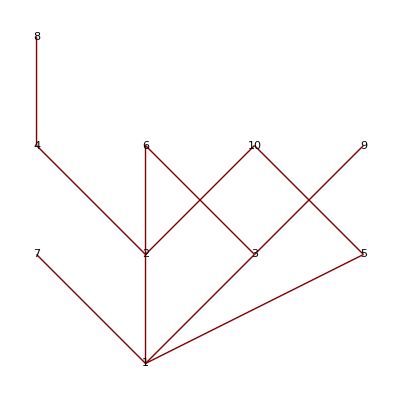

```mathematica
hassDiagram[div10]
```

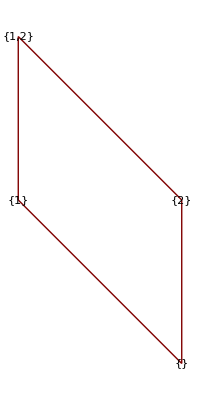

```mathematica
hassDiagram[a1]
```

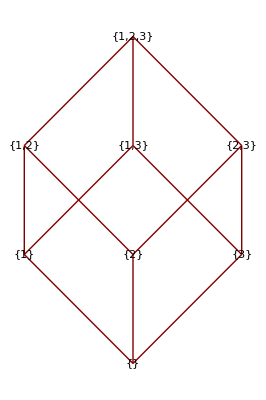

```mathematica
hassDiagram[a2]
```

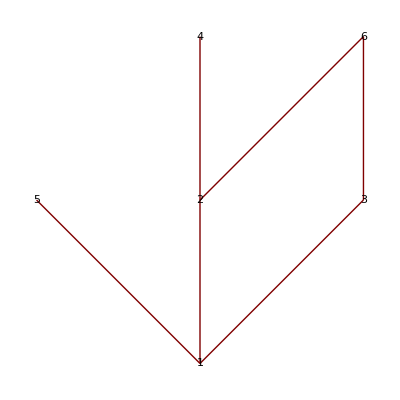

```mathematica
hassDiagram[div6]
```

```mathematica
minimalElts[R_?partialorderQ,S_List]:=Module[{M,s,t},M=S;
Do[
Do[If[MemberQ[R,{t,s}],M=Complement[M,{s}];Break[]],{t,Complement[S,{s}]}],{s,S}];M]
```

```mathematica
minimalElts[div10,Range[10]]
```

{1}

```mathematica
minimalElts[a1,Subsets[{1,2}]]
```

{{}}

```mathematica
minimalElts[div10,Range[3,10]]
```

{3,4,5,7}

```mathematica
Range[3,10]
```

{3,4,5,6,7,8,9,10}

```mathematica
minimalElts[a2,Subsets[{1,2,3}]]
```

{{}}

```mathematica
inverseRelation[R_?relationQ]:=Reverse[R,2]
```

```mathematica
maximalElts[R_?partialorderQ,S_List]:= minimalElts[inverseRelation[R],S]
```

```mathematica
maximalElts[div10,Range[10]]
```

{6,7,8,9,10}

```mathematica
maximalElts[div10,Range[10]]
```

{6,7,8,9,10}

```mathematica
maxElts[R_?partialorderQ,S_List]:=Module[{M,s,t},M=S;Do[
Do[
If[MemberQ[R,{s,t}],M=Complement[M,{s}];Break[]],{t,Complement[S,{s}]}],{s,S}];M]
```

```mathematica
maxElts[a2,Subsets[{1,2,3}]]
```

{{1,2,3}}

```mathematica
maxElts[div10,Range[10]]
```

{6,7,8,9,10}

```mathematica
Practical -4  Infimum and supremum
```

```mathematica
lowerBoundQ[R_?partialorderQ,S_List,l_]:=Module[{s},Catch[Do[If[!MemberQ[R,{l,s}],Throw[False];Break[]],{s,S}];Throw[True]]]
```

```mathematica
lowerBoundQ[div10,{2,3,6,7},2]
```

False

```mathematica
lowerBoundQ[div10,{2},2]
```

True

```mathematica
lowerBounds[R_?partialorderQ,S_List]:=Module[{domR},domR=findDomain[R];Select[domR,lowerBoundQ[R,S,#]&]]
```

```mathematica
lowerBounds[div10,{2,4,6}]
```

{1,2}

```mathematica
greatestlowerBound[R_?partialorderQ,S_List]:= Module[{U,M},U=lowerBounds[R,S];M=maximalElts[R,U]; If[Length[M]≠ 1,"Does not exists",M[[1]]]]
```

```mathematica
greatestlowerBound[div10,{2,4,6}]
```

2

```mathematica
upperBoundQ[R_?partialorderQ,S_List,u_]:=Module[{s},Catch[Do[If[!MemberQ[R,{s,u}],Throw[False];Break[]],{s,S}];Throw[True]]]

div6=dividesRelation[6]
```

dividesRelation[6]

```mathematica
upperBoundQ[div6,{1,2,3},6]
```

True

```mathematica
upperBoundQ[div6,{1,2,3,4},6]
```

False

```mathematica
upperBounds[R_?partialorderQ,S_List]:=Module[{domR},domR=findDomain[R];Select[domR,upperBoundQ[R,S,#]&]]
```

```mathematica
upperBounds[div6,{4,5}]
```

{}

```mathematica
upperBounds[div6,{1,2}]
```

{2,4,6}

```mathematica
leastupperBound[R_?partialorderQ,S_List]:= Module[{U,M},U=upperBounds[R,S];M=minimalElts[R,U]; If[Length[M]≠ 1,"Does not exists",M[[1]]]]
```

```mathematica
leastupperBound[div6,{1,2}]
```

2

```mathematica
leastupperBound[div6,{1,2,3}]
```

6

```mathematica
leastupperBound[div6,{4,5}]
```

Does not exists

```mathematica
leastupperBound[a2,{{},{1,2},{1,3}}]
```

```mathematica
{1,2,3}

Practical - 5 Lattice
```

```mathematica
?===
```

RowBox[{StyleBox["lhs", "TI"], "===", StyleBox["rhs", "TI"]}] yields True if the expression StyleBox["lhs", "TI"] is identical to StyleBox["rhs", "TI"], and yields False otherwise.

```mathematica
t-1 === 1
```

False

```mathematica
x=2
```

2

```mathematica
x-1==1
```

True

```mathematica
?==
```

lhs==rhs returns True if lhs and rhs are identical.

```mathematica
x-1==3
```

False

```mathematica
x-1===1
```

True

```mathematica
hasLUBs[R_?partialorderQ]:= Module[{domR,a,b},domR=findDomain[R]; Catch[Do[If[leastupperBound[R,{a,b}]==="Does not exists",Throw[False]],{a,domR},{b,domR}];Throw[True]]]
```

```mathematica
hasGLBs[R_?partialorderQ]:= Module[{domR,a,b},domR=findDomain[R]; Catch[Do[If[greatestlowerBound[R,{a,b}]==="Does not exists",Throw[False]],{a,domR},{b,domR}];Throw[True]]]
```

```mathematica
hasGLB1s[R_?partialorderQ]:= hasLUBs[inverseRelation[R]]
```

```mathematica
latticeQ[R_?partialorderQ]:= hasLUBs[R]&& hasGLBs[R]
```

```mathematica
latticeQ[dividesRelation[4]]
```

False

```mathematica
d20=dividesRelation[Divisors[20]]
```

{{1,1},{1,2},{1,4},{1,5},{1,10},{1,20},{2,2},{2,4},{2,10},{2,20},{4,4},{4,20},{5,5},{5,10},{5,20},{10,10},{10,20},{20,20}}

```mathematica
latticeQ[d20]
```

True

```mathematica
latticeQ[a2]
```

True

```mathematica
latticeQ[dividesRelation[6]]
```

False

```mathematica
Practical - 6
Basics
```

```mathematica
Logical operations : && (AND),||(OR),!(NOT)
```

```mathematica
True || False
```

True

```mathematica
True||True
```

True

```mathematica
False||True
```

True

```mathematica
False||False
```

False

```mathematica
True && True
```

True

```mathematica
True && False
```

False

```mathematica
False&& True
```

False

```mathematica
False&&False
```

False

```mathematica
!True
```

False

```mathematica
! False
```

True

```mathematica
! True&& False
```

False

```mathematica
!True||False
```

False

```mathematica
True && !True
```

False

```mathematica
True ∨ False
```

True

```mathematica
True ∧ False
```

False

```mathematica
¬ True
```

False

```mathematica
Representing Boolean Functions
1. f(x,y,z)=xy+yz+xz
```

```mathematica
f[x_,y_,z_]:=(x∧y)∨(y∧z)∨(z∧x);
f[p,q,r]
```

(p&&q)||(q&&r)||(r&&p)

```mathematica
f[True,False,True]
```

True

```mathematica
f[True,q,r]
```

q||(q&&r)||r

```mathematica
f[True,q,r]//Simplify
```

q||r

```mathematica
2. g(x,y)=!(!(x+y)x+!!!y)+xy+x!y
```

```mathematica
g[x_,y_]:=!((!(x∨y)∧x)∨ !!!y)∨ (x∧y)∨(x∧!y)
g[False,False]
```

False

```mathematica
g[False,True]
```

True

```mathematica
g[True,False]
```

True

```mathematica
g[True,True]
```

True

```mathematica
3. h(x,y,z)=x(!(y+z))+(xy+!z)x
```

```mathematica
h[x_,y_,z_]:=(x∧(!(y∨ z)))∨ ((x∧y)∨ !z)∧x;
h[0,0,0]//Simplify
```

False

```mathematica
h[1,0,0]//Simplify
h[0,1,0]//Simplify
h[0,0,1]//Simplify
h[1,1,0]//Simplify
h[0,1,1]//Simplify
h[1,0,1]//Simplify
h[1,1,1]//Simplify
```

True

False

False

True

False

False

True

Table Form
1. For Boolean Expression f:

```mathematica
BooleanTable[{p,q,r,f[p,q,r]},{p,q,r}]
```

{{True,True,True,True},{True,True,False,True},{True,False,True,True},{True,False,False,False},{False,True,True,True},{False,True,False,False},{False,False,True,False},{False,False,False,False}}

```mathematica
BooleanTable[{p,q,r,f[p,q,r]},{p,q,r}]//TableForm
```

True | True | True | True
True | True | False | True
True | False | True | True
True | False | False | False
False | True | True | True
False | True | False | False
False | False | True | False
False | False | False | False

```mathematica
Boole[BooleanTable[{p,q,r,f[p,q,r]},{p,q,r}]]//TableForm
```

1 | 1 | 1 | 1
1 | 1 | 0 | 1
1 | 0 | 1 | 1
1 | 0 | 0 | 0
0 | 1 | 1 | 1
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 0

```mathematica
TableForm[Boole[BooleanTable[{p,q,r,f[p,q,r]},{p,q,r}]],TableHeadings->{None,{p,q,r,f}}]
```

p | q | r | f
1 | 1 | 1 | 1
1 | 1 | 0 | 1
1 | 0 | 1 | 1
1 | 0 | 0 | 0
0 | 1 | 1 | 1
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 0

```mathematica
2. For Boolean Expression g:
```

```mathematica
TableForm[Boole[BooleanTable[{p,q,g[p,q]},{p,q}]],TableHeadings->{None,{p,q,g}}]
```

p | q | g
1 | 1 | 1
1 | 0 | 1
0 | 1 | 1
0 | 0 | 1

```mathematica
3. For Boolean Expression h:
```

```mathematica
TableForm[Boole[BooleanTable[{p,q,r,h[p,q,r]},{p,q,r}]],TableHeadings->{None,{p,q,r,h}}]
```

p | q | r | h
1 | 1 | 1 | 1
1 | 1 | 0 | 1
1 | 0 | 1 | 0
1 | 0 | 0 | 1
0 | 1 | 1 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 0

```mathematica
Practical 7
```

```mathematica
1. Dual of a Boolean polynomial/ expression
```

```mathematica
dual[expr_]:= expr/.{And-> Or,Or-> And, False-> True, True-> False}
dual [f[p,q,r]]
```

(p||q)&&(q||r)&&(r||p)

```mathematica
%//Simplify
```

(p&&(q||r))||(q&&r)

```mathematica
dual[g[p,q]]
```

!((!(p&&q)||p)&&!q)&&(p||q)&&(p||!q)

```mathematica
%//Simplify
```

p&&q

```mathematica
dual[h[p,q,r]]
```

(p||!(q&&r))&&(((p||q)&&!r)||p)

```mathematica
%//Simplify
```

p||(q&&!r)

```mathematica
2. Whether or not two given Boolean polynomials are equivalent
Let us enter the Boolean polynomial j(x,y,z) = x(y+z)+yz and check if it is equivalent to f(x,y,z)
```

```mathematica
j[x_,y_,z_]:= (x∧ (y∨ z))∨(y∧z);
Boole[BooleanTable[{p,q,r,j[p,q,r]},{p,q,r}]]//TableForm
```

1 | 1 | 1 | 1
1 | 1 | 0 | 1
1 | 0 | 1 | 1
1 | 0 | 0 | 0
0 | 1 | 1 | 1
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 0

```mathematica
We can see that the boolean polynomial function f and j are same,hence they are equivalent.
```

```mathematica
However,boolean polynomial function h and f are different, hence they are not equivalent.
```

```mathematica
3. Disjunctive Normal form (Conjunctive Normal Form) from a boolean expression:
j(x,y,z) = x(y+z)+yz
```

```mathematica
Clear[x]
j[x_,y_,z_]= (x∧ (y∨ z))∨(y∧z)
BooleanConvert[j[p,q,r],"DNF"]
BooleanConvert[j[p,q,r],"CNF"]
```

(x&&(y||z))||(y&&z)

(p&&q)||(p&&r)||(q&&r)

(p||q)&&(p||r)&&(q||r)

```mathematica
DNF refers to Disjunctive Normal Form (Sum of Products Form)
CNF refers to Conjunctive Normal Form (Products of Sums Form)
```

```mathematica
k[x_,y_,z_]:= (x∨y)∧!z;
k[x_,y_,z_]= (x∨y)∧!z
BooleanConvert[k[p,q,r],"DNF"]
BooleanConvert[k[p,q,r],"CNF"]
```

(x||y)&&!z

(p&&!r)||(q&&!r)

(p||q)&&!r

```mathematica
f[x_,y_,z_]=(x∧y)∨(y∧z)∨(z∧x)
BooleanConvert[f[p,q,r],"DNF"]
BooleanConvert[f[p,q,r],"CNF"]
```

(x&&y)||(y&&z)||(z&&x)

(p&&q)||(p&&r)||(q&&r)

(p||q)&&(p||r)&&(q||r)

```mathematica
g[x_,y_]=!((!(x∨y)∧x)∨ !!!y)∨ (x∧y)∨(x∧!y)
BooleanConvert[g[p,q],"DNF"]
BooleanConvert[g[p,q],"CNF"]
```

!((!(x||y)&&x)||!y)||(x&&y)||(x&&!y)

p||q

p||q

```mathematica
h[x_,y_,z_]=(x∧(!(y∨ z)))∨ ((x∧y)∨ !z)∧x
BooleanConvert[h[p,q,r],"DNF"]
BooleanConvert[h[p,q,r],"CNF"]
```

(x&&!(y||z))||(((x&&y)||!z)&&x)

(p&&q)||(p&&!r)

p&&(q||!r)

```mathematica
4.  Disjunctive Normal form (Conjunctive Normal Form) when the  given boolean polynomial function is expressed by a table of values.
```

```mathematica
x|y|z|F(x,y,z)
1|1|1|0
1|1|0|1
1|0|1|0
1|0|0|1
0|1|1|0
0|1|0|1
0|0|1|1
0|0|0|0
```

```mathematica
BooleanFunction[{{1,1,0}-> 1,{1,0,0}-> 1,{0,1,0}-> 1,{0,0,1}-> 1,{__}-> 0},{x,y,z},"DNF"]
```

(x&&!z)||(!x&&!y&&z)||(y&&!z)

```mathematica
BooleanFunction[{{1,1,0}-> 1,{1,0,0}-> 1,{0,1,0}-> 1,{0,0,1}-> 1,{__}-> 0},{x,y,z},"CNF"]
```

(!x||!z)&&(x||y||z)&&(!y||!z)

```mathematica
x|y|z|G(x,y,z)
1|1|1|0
1|1|0|0
1|0|1|0
1|0|0|1
0|1|1|1
0|1|0|0
0|0|1|0
0|0|0|1
```

```mathematica
BooleanFunction[{{1,0,0}-> 1,{0,0,0}-> 1,{0,1,1}-> 1,{__}-> 0},{x,y,z},"DNF"]
BooleanFunction[{{1,0,0}-> 1,{0,0,0}-> 1,{0,1,1}-> 1,{__}-> 0},{x,y,z},"CNF"]
```

(!x&&y&&z)||(!y&&!z)

(!x||!y)&&(!y||z)&&(y||!z)

```mathematica
Practical 8 Minimizing a given boolean expression to find minimal expressions
```

```mathematica
To obtain minimized expression in DNF, we can use BooleanMinimize
```

```mathematica
Clear[a]
BooleanMinimize[(a∧ b)∨(!a∧b∧!c)]
```

(a&&b)||(b&&!c)

```mathematica
To obtain minimized expression in CNF, we can use BooleanMinimize with specification for CNF as under
```

```mathematica
BooleanMinimize[(a∧ b)∨(!a∧b∧!c),"CNF"]
```

(a||!c)&&b

```mathematica
To obtain minimized expression in whichever form as minimum length, we can use simplify
```

```mathematica
Simplify[(a∧ b)∨(!a∧b∧!c)]
```

(a||!c)&&b

```mathematica
1.(x+y)(x+z)+xyz
```

```mathematica
BooleanMinimize[(x∨y)∧(x∨z)∨(x∧y∧z)]
```

x||(y&&z)

```mathematica
2. xyz' +xy'z+x'yz+x'y'z'+x'z
```

```mathematica
BooleanMinimize[(x∧y∧!z)∨(x∧!y∧z)∨(!x∧y∧z)∨(!x∧!y∧!z)∨(!x∧z)]
```

(x&&y&&!z)||(!x&&!y)||(!x&&z)||(!y&&z)

```mathematica
3. x'y+x'y'z+xy'z'+xyz'
```

```mathematica
BooleanMinimize[(!x∧y)∨(!x∧!y∧z)∨(x∧!y∧z)∨(x∧y∧!z)]
```

(!x&&y)||(y&&!z)||(!y&&z)

```mathematica
Practical 9
```

```mathematica
Representing a given circuit diagram ( expressed using Gates) in the form  of Boolean Expression
```

```mathematica
To give Boolean expression of the given circuit diagram we define each gate G separately, and finally ask for the value of the output G1.
```

```mathematica
Clear[a,b,c]
G4=¬a;
G5=¬c;
G2=a∧b;
G3=G4∧G5∧b;
G1=G2∨G3;
G1
```

(a&&b)||(!a&&!c&&b)

```mathematica
Clear[A,B]
G2=A∧B∧C;
G4=¬C;
G3=A∧B∧G4;
G5=¬A;
G6=¬C;
G7=G5∧B∧G6;
G1=G2∨G3∨G7;
G1
```

(A&&B&&C)||(A&&B&&!C)||(!A&&B&&!C)